```mathematica
(*Creating a random bivariate polynomial and finding its length upto a constant*)
(*This portion of the code takes a long long time to run, it is better to use copy paste
the values in the output to the lenCur array manually*)
n=2;
lenCur = ConstantArray[0,{20,9}];
lenCur
For[n=2,n≤10,n++,
Print[n*100];
For[count=1,count≤20,count++,
Print[count];
Coeffs = RandomVariate[NormalDistribution[], {(4n+2),2n+2}];
a=Coeffs[[1;;2n+1,1;;n+1]];
aI=Coeffs[[1;;2n+1,n+2;;2n+2]];
b=Coeffs[[2n+2;;4n+2,1;;n+1]];
bI=Coeffs[[2n+2;;4n+2,n+2;;2n+2]];
f[s_,t_]=Sum[a[[k+n+1,l+1]]*Cos[(k)*s+ (l)*t]+ aI[[k+n+1,l+1]]*Sin[(k)*s+ (l)*t],{k,-n,n},{l,0,n}];
g[s_,t_]=Sum[b[[k+n+1,l+1]]*Cos[(k)*s +(l)*t]+bI[[k+n+1,l+1]]*Sin[(k)*s+ (l)*t],{k,-n,n},{l,0,n}];

(*Compute the Det of Jacobian*)
DJ[s_,t_]=Det[{{D[f[s,t],s],D[f[s,t],t]},{D[g[s,t],s],D[g[s,t],t]}}];
(*Find the Critical curve*)
(*CritCurve=Solve[DJ[x,y]==0,{x,y},Reals];*)
image = ContourPlot[DJ[x,y]==0,{x,0,6.283},{y,0,6.283},Axes->False];
imageMat = ImageData[image];
(*Estimate length by averaging number of intersections of horizontal lines with the critical curve (Buffon's needle trick).
This gives the length upto a constant.*)
For[i=1,i≤Dimensions[imageMat][[1]],i++,For[j=1,j≤Dimensions[imageMat][[2]],j++,If[imageMat[[i,j,1]]<0.85||imageMat[[i,j,2]]<0.85||imageMat[[i,j,3]]<0.85,lenCur[[count,n-1]]=lenCur[[count,n-1]]+1,0]]]
];
Print[lenCur];]
lenCur
N[Mean[lenCur]]
(*
Length[Solve[DJ[x,0.5]==0 && 0 ≤ x && x≤6.283,{x}]]+
Length[Solve[DJ[x,0.2]==0 && 0 ≤ x && x≤6.283,{x}]]+
Length[Solve[DJ[x,1]==0 && 0 ≤ x && x≤6.283,{x}]]+
Length[Solve[DJ[x,1.5]==0 && 0 ≤ x && x≤6.283,{x}]]+
Length[Solve[DJ[x,3.5]==0 && 0 ≤ x && x≤6.283,{x}]]
*)
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

200

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

{{12074,0,0,0,0,0,0,0,0},{13257,0,0,0,0,0,0,0,0},{13048,0,0,0,0,0,0,0,0},{10793,0,0,0,0,0,0,0,0},{11724,0,0,0,0,0,0,0,0},{12085,0,0,0,0,0,0,0,0},{11559,0,0,0,0,0,0,0,0},{12096,0,0,0,0,0,0,0,0},{12389,0,0,0,0,0,0,0,0},{12929,0,0,0,0,0,0,0,0},{11909,0,0,0,0,0,0,0,0},{13292,0,0,0,0,0,0,0,0},{12350,0,0,0,0,0,0,0,0},{13279,0,0,0,0,0,0,0,0},{11510,0,0,0,0,0,0,0,0},{12004,0,0,0,0,0,0,0,0},{11248,0,0,0,0,0,0,0,0},{12090,0,0,0,0,0,0,0,0},{12391,0,0,0,0,0,0,0,0},{11833,0,0,0,0,0,0,0,0}}

300

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

{{12074,15979,0,0,0,0,0,0,0},{13257,17046,0,0,0,0,0,0,0},{13048,16402,0,0,0,0,0,0,0},{10793,16811,0,0,0,0,0,0,0},{11724,17045,0,0,0,0,0,0,0},{12085,15812,0,0,0,0,0,0,0},{11559,16708,0,0,0,0,0,0,0},{12096,15834,0,0,0,0,0,0,0},{12389,15971,0,0,0,0,0,0,0},{12929,15744,0,0,0,0,0,0,0},{11909,14067,0,0,0,0,0,0,0},{13292,16452,0,0,0,0,0,0,0},{12350,15263,0,0,0,0,0,0,0},{13279,16004,0,0,0,0,0,0,0},{11510,16372,0,0,0,0,0,0,0},{12004,16413,0,0,0,0,0,0,0},{11248,15410,0,0,0,0,0,0,0},{12090,15769,0,0,0,0,0,0,0},{12391,16645,0,0,0,0,0,0,0},{11833,16887,0,0,0,0,0,0,0}}

400

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

{{12074,15979,19323,0,0,0,0,0,0},{13257,17046,20176,0,0,0,0,0,0},{13048,16402,20270,0,0,0,0,0,0},{10793,16811,19925,0,0,0,0,0,0},{11724,17045,18971,0,0,0,0,0,0},{12085,15812,20389,0,0,0,0,0,0},{11559,16708,20083,0,0,0,0,0,0},{12096,15834,19372,0,0,0,0,0,0},{12389,15971,19984,0,0,0,0,0,0},{12929,15744,19949,0,0,0,0,0,0},{11909,14067,20488,0,0,0,0,0,0},{13292,16452,20151,0,0,0,0,0,0},{12350,15263,20455,0,0,0,0,0,0},{13279,16004,19032,0,0,0,0,0,0},{11510,16372,21116,0,0,0,0,0,0},{12004,16413,19454,0,0,0,0,0,0},{11248,15410,20897,0,0,0,0,0,0},{12090,15769,20019,0,0,0,0,0,0},{12391,16645,19220,0,0,0,0,0,0},{11833,16887,19395,0,0,0,0,0,0}}

500

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

{{12074,15979,19323,22496,0,0,0,0,0},{13257,17046,20176,23990,0,0,0,0,0},{13048,16402,20270,23566,0,0,0,0,0},{10793,16811,19925,23356,0,0,0,0,0},{11724,17045,18971,24051,0,0,0,0,0},{12085,15812,20389,22875,0,0,0,0,0},{11559,16708,20083,24649,0,0,0,0,0},{12096,15834,19372,23410,0,0,0,0,0},{12389,15971,19984,22633,0,0,0,0,0},{12929,15744,19949,23716,0,0,0,0,0},{11909,14067,20488,24182,0,0,0,0,0},{13292,16452,20151,24171,0,0,0,0,0},{12350,15263,20455,24304,0,0,0,0,0},{13279,16004,19032,24077,0,0,0,0,0},{11510,16372,21116,23868,0,0,0,0,0},{12004,16413,19454,23622,0,0,0,0,0},{11248,15410,20897,24021,0,0,0,0,0},{12090,15769,20019,24174,0,0,0,0,0},{12391,16645,19220,22725,0,0,0,0,0},{11833,16887,19395,22945,0,0,0,0,0}}

600

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

{{12074,15979,19323,22496,28399,0,0,0,0},{13257,17046,20176,23990,28384,0,0,0,0},{13048,16402,20270,23566,27018,0,0,0,0},{10793,16811,19925,23356,28610,0,0,0,0},{11724,17045,18971,24051,28835,0,0,0,0},{12085,15812,20389,22875,28699,0,0,0,0},{11559,16708,20083,24649,27739,0,0,0,0},{12096,15834,19372,23410,28280,0,0,0,0},{12389,15971,19984,22633,27804,0,0,0,0},{12929,15744,19949,23716,27431,0,0,0,0},{11909,14067,20488,24182,27826,0,0,0,0},{13292,16452,20151,24171,27019,0,0,0,0},{12350,15263,20455,24304,28494,0,0,0,0},{13279,16004,19032,24077,26547,0,0,0,0},{11510,16372,21116,23868,27810,0,0,0,0},{12004,16413,19454,23622,28535,0,0,0,0},{11248,15410,20897,24021,27353,0,0,0,0},{12090,15769,20019,24174,28000,0,0,0,0},{12391,16645,19220,22725,26101,0,0,0,0},{11833,16887,19395,22945,27938,0,0,0,0}}

700

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

{{12074,15979,19323,22496,28399,31326,0,0,0},{13257,17046,20176,23990,28384,31678,0,0,0},{13048,16402,20270,23566,27018,31259,0,0,0},{10793,16811,19925,23356,28610,32380,0,0,0},{11724,17045,18971,24051,28835,32865,0,0,0},{12085,15812,20389,22875,28699,32553,0,0,0},{11559,16708,20083,24649,27739,31579,0,0,0},{12096,15834,19372,23410,28280,31924,0,0,0},{12389,15971,19984,22633,27804,31803,0,0,0},{12929,15744,19949,23716,27431,31184,0,0,0},{11909,14067,20488,24182,27826,31719,0,0,0},{13292,16452,20151,24171,27019,31135,0,0,0},{12350,15263,20455,24304,28494,31073,0,0,0},{13279,16004,19032,24077,26547,31820,0,0,0},{11510,16372,21116,23868,27810,32455,0,0,0},{12004,16413,19454,23622,28535,32532,0,0,0},{11248,15410,20897,24021,27353,32837,0,0,0},{12090,15769,20019,24174,28000,33444,0,0,0},{12391,16645,19220,22725,26101,32364,0,0,0},{11833,16887,19395,22945,27938,32021,0,0,0}}

800

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

{{12074,15979,19323,22496,28399,31326,35652,0,0},{13257,17046,20176,23990,28384,31678,36915,0,0},{13048,16402,20270,23566,27018,31259,36432,0,0},{10793,16811,19925,23356,28610,32380,34290,0,0},{11724,17045,18971,24051,28835,32865,36217,0,0},{12085,15812,20389,22875,28699,32553,35681,0,0},{11559,16708,20083,24649,27739,31579,35780,0,0},{12096,15834,19372,23410,28280,31924,36665,0,0},{12389,15971,19984,22633,27804,31803,36062,0,0},{12929,15744,19949,23716,27431,31184,35106,0,0},{11909,14067,20488,24182,27826,31719,36404,0,0},{13292,16452,20151,24171,27019,31135,35581,0,0},{12350,15263,20455,24304,28494,31073,35451,0,0},{13279,16004,19032,24077,26547,31820,35494,0,0},{11510,16372,21116,23868,27810,32455,34808,0,0},{12004,16413,19454,23622,28535,32532,35713,0,0},{11248,15410,20897,24021,27353,32837,35453,0,0},{12090,15769,20019,24174,28000,33444,36225,0,0},{12391,16645,19220,22725,26101,32364,34512,0,0},{11833,16887,19395,22945,27938,32021,35377,0,0}}

900

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

{{12074,15979,19323,22496,28399,31326,35652,40719,0},{13257,17046,20176,23990,28384,31678,36915,40867,0},{13048,16402,20270,23566,27018,31259,36432,40007,0},{10793,16811,19925,23356,28610,32380,34290,39939,0},{11724,17045,18971,24051,28835,32865,36217,39655,0},{12085,15812,20389,22875,28699,32553,35681,40558,0},{11559,16708,20083,24649,27739,31579,35780,38808,0},{12096,15834,19372,23410,28280,31924,36665,39230,0},{12389,15971,19984,22633,27804,31803,36062,39833,0},{12929,15744,19949,23716,27431,31184,35106,39624,0},{11909,14067,20488,24182,27826,31719,36404,39937,0},{13292,16452,20151,24171,27019,31135,35581,40168,0},{12350,15263,20455,24304,28494,31073,35451,40505,0},{13279,16004,19032,24077,26547,31820,35494,38523,0},{11510,16372,21116,23868,27810,32455,34808,39069,0},{12004,16413,19454,23622,28535,32532,35713,38998,0},{11248,15410,20897,24021,27353,32837,35453,39920,0},{12090,15769,20019,24174,28000,33444,36225,39653,0},{12391,16645,19220,22725,26101,32364,34512,39559,0},{11833,16887,19395,22945,27938,32021,35377,39886,0}}

1000

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

{{12074,15979,19323,22496,28399,31326,35652,40719,42974},{13257,17046,20176,23990,28384,31678,36915,40867,43791},{13048,16402,20270,23566,27018,31259,36432,40007,43419},{10793,16811,19925,23356,28610,32380,34290,39939,44001},{11724,17045,18971,24051,28835,32865,36217,39655,42997},{12085,15812,20389,22875,28699,32553,35681,40558,42925},{11559,16708,20083,24649,27739,31579,35780,38808,43153},{12096,15834,19372,23410,28280,31924,36665,39230,43436},{12389,15971,19984,22633,27804,31803,36062,39833,43550},{12929,15744,19949,23716,27431,31184,35106,39624,43078},{11909,14067,20488,24182,27826,31719,36404,39937,44285},{13292,16452,20151,24171,27019,31135,35581,40168,44790},{12350,15263,20455,24304,28494,31073,35451,40505,43303},{13279,16004,19032,24077,26547,31820,35494,38523,44350},{11510,16372,21116,23868,27810,32455,34808,39069,42711},{12004,16413,19454,23622,28535,32532,35713,38998,42228},{11248,15410,20897,24021,27353,32837,35453,39920,43519},{12090,15769,20019,24174,28000,33444,36225,39653,42943},{12391,16645,19220,22725,26101,32364,34512,39559,41850},{11833,16887,19395,22945,27938,32021,35377,39886,43651}}

{{12074,15979,19323,22496,28399,31326,35652,40719,42974},{13257,17046,20176,23990,28384,31678,36915,40867,43791},{13048,16402,20270,23566,27018,31259,36432,40007,43419},{10793,16811,19925,23356,28610,32380,34290,39939,44001},{11724,17045,18971,24051,28835,32865,36217,39655,42997},{12085,15812,20389,22875,28699,32553,35681,40558,42925},{11559,16708,20083,24649,27739,31579,35780,38808,43153},{12096,15834,19372,23410,28280,31924,36665,39230,43436},{12389,15971,19984,22633,27804,31803,36062,39833,43550},{12929,15744,19949,23716,27431,31184,35106,39624,43078},{11909,14067,20488,24182,27826,31719,36404,39937,44285},{13292,16452,20151,24171,27019,31135,35581,40168,44790},{12350,15263,20455,24304,28494,31073,35451,40505,43303},{13279,16004,19032,24077,26547,31820,35494,38523,44350},{11510,16372,21116,23868,27810,32455,34808,39069,42711},{12004,16413,19454,23622,28535,32532,35713,38998,42228},{11248,15410,20897,24021,27353,32837,35453,39920,43519},{12090,15769,20019,24174,28000,33444,36225,39653,42943},{12391,16645,19220,22725,26101,32364,34512,39559,41850},{11833,16887,19395,22945,27938,32021,35377,39886,43651}}

{12193.,16131.7,19933.5,23641.6,27841.1,31997.6,35690.9,39772.9,43347.7}

```mathematica
lenCur
WriteString["~/data_new.csv",ExportString[lenCur,"CSV"]]
```

{{12074,15979,19323,22496,28399,31326,35652,40719,42974},{13257,17046,20176,23990,28384,31678,36915,40867,43791},{13048,16402,20270,23566,27018,31259,36432,40007,43419},{10793,16811,19925,23356,28610,32380,34290,39939,44001},{11724,17045,18971,24051,28835,32865,36217,39655,42997},{12085,15812,20389,22875,28699,32553,35681,40558,42925},{11559,16708,20083,24649,27739,31579,35780,38808,43153},{12096,15834,19372,23410,28280,31924,36665,39230,43436},{12389,15971,19984,22633,27804,31803,36062,39833,43550},{12929,15744,19949,23716,27431,31184,35106,39624,43078},{11909,14067,20488,24182,27826,31719,36404,39937,44285},{13292,16452,20151,24171,27019,31135,35581,40168,44790},{12350,15263,20455,24304,28494,31073,35451,40505,43303},{13279,16004,19032,24077,26547,31820,35494,38523,44350},{11510,16372,21116,23868,27810,32455,34808,39069,42711},{12004,16413,19454,23622,28535,32532,35713,38998,42228},{11248,15410,20897,24021,27353,32837,35453,39920,43519},{12090,15769,20019,24174,28000,33444,36225,39653,42943},{12391,16645,19220,22725,26101,32364,34512,39559,41850},{11833,16887,19395,22945,27938,32021,35377,39886,43651}}

```mathematica
(*Compute the averages of the lengths*)
MeanLen = N[Mean[lenCur]]
AvgLen = ConstantArray[0,{9,2}];
For[i=2,i≤10,i++,AvgLen[[i-1,1]]=i;AvgLen[[i-1,2]]=MeanLen[[i-1]]
];
AvgLen
(*AvgLen = {{2,12193},{3,16131.7},{4,19933.45},{5,23641.55},{6,27841.1},{7,31997.55},{8,35690.9},{9,39772.9},{10,43347.7}}*)
```

{12193.,16131.7,19933.5,23641.6,27841.1,31997.6,35690.9,39772.9,43347.7}

{{2,12193.},{3,16131.7},{4,19933.5},{5,23641.6},{6,27841.1},{7,31997.6},{8,35690.9},{9,39772.9},{10,43347.7}}

4297.54+3923.56 x

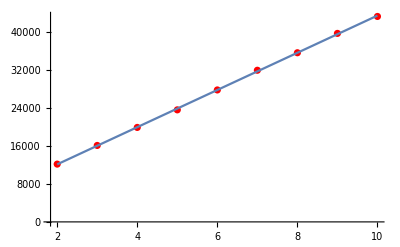

```mathematica
line=Fit[AvgLen,{1,x},x]
Show[ListPlot[AvgLen,PlotStyle->Red],Plot[{line},{x,2,10}]]
```

```mathematica
(*Calibration of length using a circle*)
image = ContourPlot[(x-3)^2+(y-3)^2==1.6*1.6,{x,0,6.283},{y,0,6.283},Axes->False]
lens=0
imageMat = ImageData[image];
For[i=1,i≤Dimensions[imageMat][[1]],i++,For[j=1,j≤Dimensions[imageMat][[2]],j++,If[imageMat[[i,j,1]]<0.85||imageMat[[i,j,2]]<0.85||imageMat[[i,j,3]]<0.85,lens=lens+1,0]]]
lens
```

{{1,3868},{1.2,4097},{1.6,4580},{1.414,4337},{1.732,4705},{2,5034},{2.236,5311},{2.449,5606},{2.646,5840},{2.828,6025},{3,6214}}

2668.53+1188.11 x

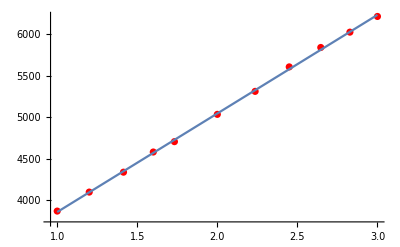

```mathematica
(* These values were obtained by repeating the code block above for different radii*)
circleLen={{1,3868},{1.2,4097},{1.6,4580},{1.414,4337},{1.732,4705},{2,5034},{2.236,5311},{2.449,5606},{2.646,5840},{2.828,6025},{3,6214}}
line=Fit[circleLen,{1,x},x]
Show[ListPlot[circleLen,PlotStyle->Red],Plot[{line},{x,1,3}]]
```

{{2,12193.},{3,16131.7},{4,19933.5},{5,23641.6},{6,27841.1},{7,31997.6},{8,35690.9},{9,39772.9},{10,43347.7}}

{{2,8.01649},{3,11.3316},{4,14.5314},{5,17.6524},{6,21.1871},{7,24.6854},{8,27.794},{9,31.2297},{10,34.2386}}

1.3711+3.30235 x

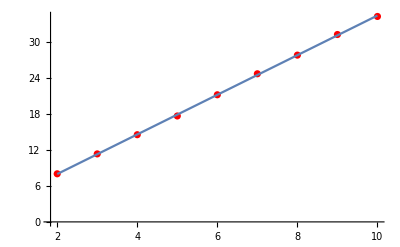

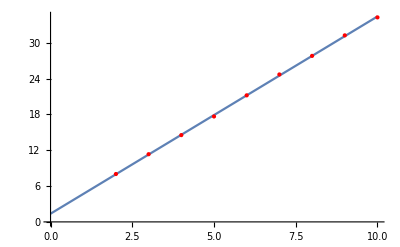

```mathematica
calibAvgLen=AvgLen
(*The way we have calibrated using the circles, we need to multiply by 2Pi to get the actual length
of the curve. However, the flat torus is itself scaled by a factor of 2Pi in our code, and we haven't
done this scaling in the paper. So we need to divide by a factor of 2Pi to get the actual length obtained
in the paper. These two effects cancel off below while computing the calibrated
average length. *)
For[i=1,i≤Dimensions[AvgLen][[1]],i++,calibAvgLen[[i,2]]=(AvgLen[[i,2]]-2668.53)/1188.11]
calibAvgLen
(*The slope of this line is approximately 3.3*)
line=Fit[calibAvgLen,{1,x},x]
Show[ListPlot[calibAvgLen,PlotStyle->Red],Plot[{line},{x,2,10}]]
Plot[line,{x,0,10},Epilog->{Red,PointSize[Medium],Point[calibAvgLen]}]
```

```mathematica
(*Determine the slope theoretically using Monte Carlo*)
V = {{1/5,0,1/9,0,0 },
{0,1/9,0,0,0},
{1/9,0,1/5,0,0},
{0,0,0,1,0},
{0,0,0,0,1}};
V//MatrixForm
EV=Eigenvectors[V];
EV[[3,1;;5]]=1/Sqrt[2] EV[[3,1;;5]];
EV[[5,1;;5]]=1/Sqrt[2] EV[[5,1;;5]];
EV.Transpose[EV];
Lambda = Sqrt[EV.V.Transpose[EV]];
Lambda//MatrixForm
SqRtV = Lambda.EV;
Transpose[SqRtV]//MatrixForm
Transpose[SqRtV].SqRtV//MatrixForm
count=200000
samples = RandomVariate[NormalDistribution[], {count,5}];
For[i=1,i≤count,i++,
samples[[i,1;;5]]=Transpose[SqRtV].samples[[i,1;;5]]]
samples//MatrixForm;
LenArr=ConstantArray[0,count];
For[i=1,i≤count,i++,
a=samples[[i,1]];
b=samples[[i,2]];
c=samples[[i,3]];
v1=samples[[i,4]];
v2=samples[[i,5]];
LenArr[[i]]=Sqrt[(c*v1-b*v2)^2+(-b*v1+a*v2)^2]
]
LenArr;
(*This is the theoretical scaling factor which will also be close to 3.3*)
Sqrt[3]*Pi*Mean[LenArr]
```

(1/5 | 0 | 1/9 | 0 | 0
0 | 1/9 | 0 | 0 | 0
1/9 | 0 | 1/5 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | (√(14/5))/3 | 0 | 0
0 | 0 | 0 | 1/3 | 0
0 | 0 | 0 | 0 | 2/(3 √5))

(0 | 0 | (√(7/5))/3 | 0 | -(√(2/5))/3
0 | 0 | 0 | 1/3 | 0
0 | 0 | (√(7/5))/3 | 0 | (√(2/5))/3
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

(1/5 | 0 | 1/9 | 0 | 0
0 | 1/9 | 0 | 0 | 0
1/9 | 0 | 1/5 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

200000

3.29527